```mathematica
a=Import["/Users/stevenschowalter/desktop/mms2-5.txt.txt","Data"];
```

```mathematica
b= Drop[a,2];
```

```mathematica
c= Flatten[Take[b,All,-1]];
```

```mathematica
{num}=Dimensions[c];
```

```mathematica
step=.2;
k=0;
x=1;
```

```mathematica
stoop=Table[0,{i,20/step}];
```

```mathematica
Do[
{
Do[
If[c[[i]]≥k*step&&c[[i]]<(k+1)*step,
{
x++;
}
],{i,1,2425}];
stoop[[k+1]]={(2k+1)/2*step,x};
x=0;
}
,{k,0,20/step-1}
]
```

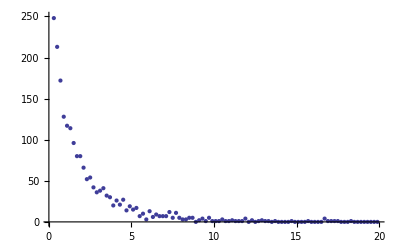

```mathematica
datpl=ListPlot[stoop,PlotRange->{0,250}]
```

```mathematica
fit=FindFit[Drop[Drop[stoop,2],-40],aa ⅇ^(-bb t),{aa,bb},t]
```

{aa→260.799,bb→0.636103}

```mathematica
fitpl=Plot[aa ⅇ^(-bb t)/.fit,{t,0,20},PlotRange->All,PlotStyle->{Red,Thickness[.01]}];
```

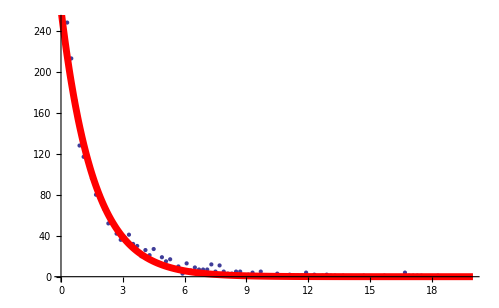

```mathematica
Show[datpl,fitpl]
```

```mathematica
(bb/.fit)^-1
```

1.57207

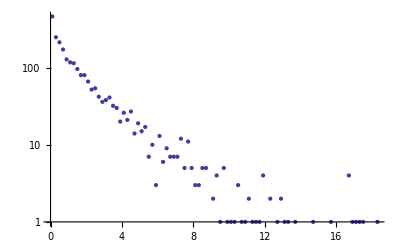

```mathematica
ListLogPlot[stoop]
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
weight=Table[√(stoop[[i]][[2]])//N,{i,100}] ;
```

```mathematica
dat=Drop[Drop[stoop,2],-40];
weights=Drop[Drop[weight,2],-10];
```

```mathematica
NonlinearRegress[dat,gg ⅇ^(- t/τ),{gg,τ},t,Weights->weights]
```

{BestFitParameters→{gg→276.069,τ→1.46209},ParameterCITable→ | Estimate | Asymptotic SE | CI
gg | 276.069 | 5.68395 | {264.77,287.368}
τ | 1.46209 | 0.0381089 | {1.38633,1.53785},EstimatedVariance→210.141,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 1.85351×10^6 | 926757.
Error | 86 | 18072.1 | 210.141
Uncorrected Total | 88 | 1.87159×10^6 | 
Corrected Total | 87 | 958841. | ,AsymptoticCorrelationMatrix→(1. | -0.855889
-0.855889 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.102286
Max Parameter-Effects | 0.425052
95. % Confidence Region | 0.567728}

```mathematica
dat
```

{{0.5,213},{0.7,172},{0.9,128},{1.1,117},{1.3,114},{1.5,96},{1.7,80},{1.9,80},{2.1,66},{2.3,52},{2.5,54},{2.7,42},{2.9,36},{3.1,38},{3.3,41},{3.5,32},{3.7,30},{3.9,20},{4.1,26},{4.3,21},{4.5,27},{4.7,14},{4.9,19},{5.1,15},{5.3,17},{5.5,7},{5.7,10},{5.9,3},{6.1,13},{6.3,6},{6.5,9},{6.7,7},{6.9,7},{7.1,7},{7.3,12},{7.5,5},{7.7,11},{7.9,5},{8.1,3},{8.3,3},{8.5,5},{8.7,5},{8.9,0},{9.1,2},{9.3,4},{9.5,1},{9.7,5},{9.9,1},{10.1,1},{10.3,1},{10.5,3},{10.7,1},{10.9,1},{11.1,2},{11.3,1},{11.5,1},{11.7,1},{11.9,4},{12.1,0},{12.3,2},{12.5,0},{12.7,1},{12.9,2},{13.1,1},{13.3,1},{13.5,0},{13.7,1},{13.9,0},{14.1,0},{14.3,0},{14.5,0},{14.7,1},{14.9,0},{15.1,0},{15.3,0},{15.5,0},{15.7,1},{15.9,0},{16.1,0},{16.3,0},{16.5,0},{16.7,4},{16.9,1},{17.1,1},{17.3,1},{17.5,1},{17.7,0},{17.9,0}}

```mathematica
stoop
```

{{0.1,461},{0.3,248},{0.5,213},{0.7,172},{0.9,128},{1.1,117},{1.3,114},{1.5,96},{1.7,80},{1.9,80},{2.1,66},{2.3,52},{2.5,54},{2.7,42},{2.9,36},{3.1,38},{3.3,41},{3.5,32},{3.7,30},{3.9,20},{4.1,26},{4.3,21},{4.5,27},{4.7,14},{4.9,19},{5.1,15},{5.3,17},{5.5,7},{5.7,10},{5.9,3},{6.1,13},{6.3,6},{6.5,9},{6.7,7},{6.9,7},{7.1,7},{7.3,12},{7.5,5},{7.7,11},{7.9,5},{8.1,3},{8.3,3},{8.5,5},{8.7,5},{8.9,0},{9.1,2},{9.3,4},{9.5,1},{9.7,5},{9.9,1},{10.1,1},{10.3,1},{10.5,3},{10.7,1},{10.9,1},{11.1,2},{11.3,1},{11.5,1},{11.7,1},{11.9,4},{12.1,0},{12.3,2},{12.5,0},{12.7,1},{12.9,2},{13.1,1},{13.3,1},{13.5,0},{13.7,1},{13.9,0},{14.1,0},{14.3,0},{14.5,0},{14.7,1},{14.9,0},{15.1,0},{15.3,0},{15.5,0},{15.7,1},{15.9,0},{16.1,0},{16.3,0},{16.5,0},{16.7,4},{16.9,1},{17.1,1},{17.3,1},{17.5,1},{17.7,0},{17.9,0},{18.1,0},{18.3,1},{18.5,0},{18.7,0},{18.9,0},{19.1,0},{19.3,0},{19.5,0},{19.7,0},{19.9,0}}

```mathematica
x=0;
Do[If[stoop[[i]][[2]]<5,Null,x++],{i,1,100}]
x
```

42

```mathematica
x=1;
list=Table[{0,0},{i,42}];
Do[If[stoop[[i]][[2]]<5,Null,{list[[x]]=stoop[[i]],x++}],{i,1,100}]
```

```mathematica
list
```

{{0.1,461},{0.3,248},{0.5,213},{0.7,172},{0.9,128},{1.1,117},{1.3,114},{1.5,96},{1.7,80},{1.9,80},{2.1,66},{2.3,52},{2.5,54},{2.7,42},{2.9,36},{3.1,38},{3.3,41},{3.5,32},{3.7,30},{3.9,20},{4.1,26},{4.3,21},{4.5,27},{4.7,14},{4.9,19},{5.1,15},{5.3,17},{5.5,7},{5.7,10},{6.1,13},{6.3,6},{6.5,9},{6.7,7},{6.9,7},{7.1,7},{7.3,12},{7.5,5},{7.7,11},{7.9,5},{8.5,5},{8.7,5},{9.7,5}}

```mathematica
weights=Table[√(list[[i]][[2]]),{i,42}];
```

```mathematica
NonlinearRegress[list,gg ⅇ^(- t/τ),{gg,τ},t,Weights->weights]
```

{BestFitParameters→{gg→465.23,τ→0.786883},ParameterCITable→ | Estimate | Asymptotic SE | CI
gg | 465.23 | 19.6841 | {425.447,505.013}
τ | 0.786883 | 0.0571939 | {0.671289,0.902476},EstimatedVariance→6490.43,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 7.14335×10^6 | 3.57168×10^6
Error | 40 | 259617. | 6490.43
Uncorrected Total | 42 | 7.40297×10^6 | 
Corrected Total | 41 | 4.13901×10^6 | ,AsymptoticCorrelationMatrix→(1. | -0.701751
-0.701751 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.350898
Max Parameter-Effects | 0.886671
95. % Confidence Region | 0.556266}